```mathematica
ClearAll["Global`*"]
```

Older stuff

Power::infy: Infinite expression 1/0. encountered.

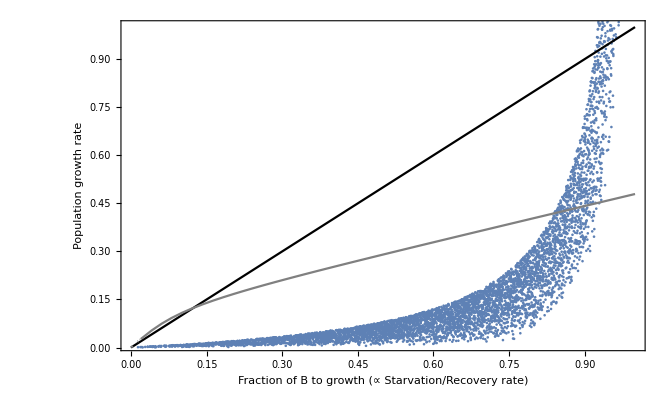

```mathematica
SppData = Table[
β=RandomReal[{0.5,1}];
(*b = RandomReal[{0.000001,0.00001}];*)
b = 0.08; (*RandomReal[{0.00002,1}];*)
ϵ=RandomReal[{1,20}];
γ0 = x;
η = 1;
{η*γ0,N[ Log[ϵ]/(1/(b*(1-β))*Log[γ0/(1-ϵ^(1-β)*(1-γ0))])]},
{x,0.0001,1,0.0001}];
Colors = {Black,Transparent,Transparent,Gray};
Show[{
ListPlot[SppData,PlotRange->{{0,1},{0.01,1}},Frame->True,FrameLabel->{"Fraction of B to growth (∝ Starvation/Recovery rate)","Population growth rate"},PlotStyle->ColorData[97,1]],
Table[Plot[λ/.Hsp[[x]],{η,0,1},PlotRange->{0,1},Frame->True,FrameLabel->{"η","λ"},PlotStyle->Colors[[x]]],{x,1,4}]
}]
```

```mathematica
Manipulate[
Show[{
LogLogPlot[c*M^(-1/4),{M,0.001,10000},PlotRange->{0,10}],
LogLogPlot[1/Log[M],{M,0.001,10000}]
}],
{c,0,10}]
```

```mathematica
Solve[c*1/Log[x] == x^(-β),x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(-ProductLog[-c β]/(c β))^(1/β)}}

```mathematica
Assuming[
```

```mathematica
Reduce[(-ProductLog[-c β]/(c β))^(1/β)≥0,c]
```

$Aborted

```mathematica
Solve[Bm/(-Em*(Log[e0]+g*Log[M]))==c*(1/Log[M]),c]
```

{{c→-(Bm Log[M])/(Em (Log[e0]+g Log[M]))}}

```mathematica
Apart[-Bm/(Em*(A + g*B)),B]
```

-Bm/(Em (A+B g))

```mathematica
Clear[FactorByVariable]
FactorByVariable[p_,c_]:=c Expand[p/c]
```

```mathematica
FactorByVariable[-Bm/(Em*(A + g*B)),B]
```

-Bm/(Em (A+B g))

After Chris has derived all of the allometric rate laws

```mathematica
λ = λ0*M^(η - 1)
σ = -Bm/(Em*Log[ϵ])
μ = -Bm/(Em*Log[ϵp])
B = B0*M^η
ρ = FullSimplify[((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*ϵ*(B0/Bm)^(1/(η-1)))^(1-η)])]
```

M^(-1+η) λ0

-Bm/(Em Log[ϵ])

-Bm/(Em Log[ϵp])

B0 M^η

(Bm (-1+η))/(Em (Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) M ϵ)^(1-η)]))

What are the qualtitative differences between these rate laws?

```mathematica
FullSimplify[M^(-1+η) λ0 <  -Bm/(Em*Log[ϵ])]
```

Em M Log[ϵ] (Bm M+Em M^η λ0 Log[ϵ])<0

```mathematica
Assuming[ϵ>0 && ϵ<1&&M>0&&Bm>0&&Em>0&&λ0>0&&η>0,FullSimplify[(Bm M+Em M^η λ0 Log[ϵ])>0]]
```

Bm M+Em M^η λ0 Log[ϵ]>0

```mathematica
Mass = 10;
λ0=RandomReal[{0,1}];
Em =RandomReal[{0.1,5}];
B0=RandomReal[{0.1,5}];
Bm =RandomReal[{0.1,B0}];
ϵ=RandomReal[{0,1}];
ϵp=ϵ*1/2;
M=Mass;
η=0.75;
Test = Bm*M > -Em*M^η*λ0*Log[ϵ];
```

```mathematica
Test
```

True

```mathematica
Mass = 10;
TimeScales=
Table[
λ0=3.39*10^-7;(*RandomReal[{0,1}];*)
Em =RandomReal[{0.1,5}];
B0=RandomReal[{0.1,5}];
Bm =RandomReal[{0.1,B0}];
ϵ=RandomReal[{0,1}];
ϵp=ϵ*1/2;
M=Mass;
η=0.75;
(*Test = Bm*M > -Em*M^η*λ0*Log[ϵ];*)
{1/λ,1/μ,1/ρ,1/σ,1/B},{1000}];
```

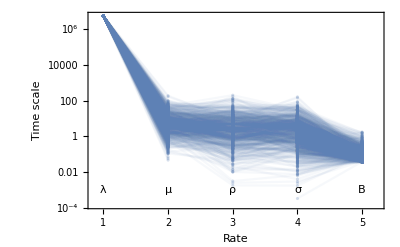

```mathematica
TimeScalePlot = Show[{
ListLogPlot[Re[TimeScales],PlotRange->{{0.85,5.25},{0.00015,All}},Joined->True,PlotStyle->Directive[{ColorData[97,1],Opacity[0.05]}],Frame->{True,True,True,True},FrameLabel->{"Rate","Time scale"}],
ListLogPlot[Re[TimeScales],PlotRange->{{0.85,5.25},All},Joined->False,PlotStyle->Directive[{ColorData[97,1],Opacity[0.25]}]],
Graphics[Style[Text["λ",{1,Log@0.001}],14]],
Graphics[Style[Text["μ",{2,Log@0.001}],14]],
Graphics[Style[Text["ρ",{3,Log@0.001}],14]],
Graphics[Style[Text["σ",{4,Log@0.001}],14]],
Graphics[Style[Text["B",{5,Log@0.001}],14]]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_TS.pdf",TimeScalePlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_TS.pdf

```mathematica
N[Count[Table[TimeScales[[All,1]][[i]]>TimeScales[[All,4]][[i]],{i,1,1000}],True]/1000]
```

0.739

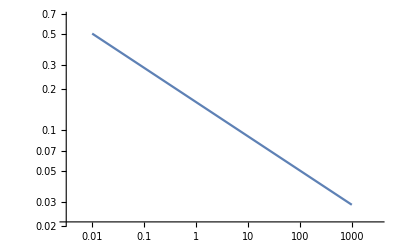

```mathematica
LogLogPlot[ λ0*M^(η - 1)/.{η->3/4,λ0->3.39*10^-7},{M,0.01,1000},PlotRange->All]
```

```mathematica
Log[1]
```

0